## Haplotypes and fitness

```mathematica
Clear["Global`*"]
```

```mathematica
makegenotype[hmat_,hpat_]:=Sort[Join[hmat,hpat]]
```

```mathematica
haplotypesF={{X,Af},{X,Am},{Xd,Af},{Xd,Am}};
```

```mathematica
haplotypesM={{X,Af},{X,Am},{Xd,Af},{Xd,Am},{Y}};
```

```mathematica
makegenotype[haplotypesF[[1]],haplotypesM[[5]]]
```

{Af,X,Y}

```mathematica
w[genotype_]:=Module[{sex,nxd,naf,w},
sex=If[Length[genotype]==4,f,m];
nxd=Count[genotype,Xd];
naf=Count[genotype,Af];
w=If[Count[{sex},f]==1,
{1-tf,1-h tf,1}[[1+naf]]*{1,1,1-cf}[[1+nxd]],
{1,1-tm}[[1+naf]]*{1,1-cm}[[1+nxd]]
];
Return[w]
]
```

```mathematica
segregation[hapNumMom_,hapNumDad_,hapNumGoal_]:=Module[{haploMom,haploDad,haploGoal,haploRec,haploNoRec,isFemale,hasDrive},
(* see what haplotypes we have *)
haploMom=haplotypesF[[hapNumMom]];
haploDad=haplotypesM[[hapNumDad]];
isFemale=haploDad!={Y};
hasDrive=Count[haploMom,Xd]==1;

(* what haplotype is desired *)
haploGoal=haplotypesM[[hapNumGoal]];

(* possible haplotypes in gametes when no recombination *)
haploNoRec={haploMom,haploDad};

(* we don't need to go through recombination if male *)
If[!isFemale,
Return[
If[hasDrive,If[Count[haploGoal,Y]==1,1-kdrive,kdrive],1/2]*Count[haploNoRec,haploGoal]
]
];

(* possible haplotypes in gametes with recombination *)
haploRec={{haploMom[[1]],haploDad[[2]]},{haploDad[[1]],haploMom[[2]]}};
Return[Simplify[Count[haploNoRec,haploGoal]/2 (1-r)+Count[haploRec,haploGoal]/2 r]]
]
```

## Recursions

Expression for W̄×y_(i,t+1):

```mathematica
WbarMytplus1=
Table[
Sum[
x[i]y[j]w[haplotypesF[[i]]]segregation[i,j,k],{i,1,Length[haplotypesF]},{j,5,5}
],{k,1,Length[haplotypesM]}
];
```

```mathematica
WbarMytplus1
```

{1/2 (1-tm) x[1] y[5],1/2 x[2] y[5],(1-cm) kdrive (1-tm) x[3] y[5],(1-cm) kdrive x[4] y[5],1/2 (1-tm) x[1] y[5]+1/2 x[2] y[5]+(1-cm) (1-kdrive) (1-tm) x[3] y[5]+(1-cm) (1-kdrive) x[4] y[5]}

```mathematica
WbarM=Total[WbarMytplus1];
```

```mathematica
ytplus1=WbarMytplus1/WbarM//Simplify;
```

```mathematica
WbarFxtplus1=Table[
Sum[
x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]]segregation[i,j,k],
{j,1,Length[haplotypesF]},{i,1,Length[haplotypesF]}
],
{k,1,Length[haplotypesF]}
];
```

```mathematica
WbarF=Total[WbarFxtplus1];
```

```mathematica
xtplus1=WbarFxtplus1/WbarF//Simplify;
```

```mathematica
WbarFxtplus1[[1]]
```

x[1] y[1]+1/2 (1-h tf) x[2] y[1]+1/2 x[3] y[1]+1/2 (1-r) (1-h tf) x[4] y[1]+1/2 (1-h tf) x[1] y[2]+1/2 r (1-h tf) x[3] y[2]+1/2 x[1] y[3]+1/2 r (1-h tf) x[2] y[3]+1/2 (1-r) (1-h tf) x[1] y[4]

```mathematica
primarySR=y[5]/(y[5]+Sum[x[i]y[j],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
secondarySR=Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]/(Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]+Sum[x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
```

## Numerical analysis (auxiliary functions)

```mathematica
iterate[{tfs_,tms_,hs_},{cfs_,cms_},{kdrives_,rs_},maxt_]:=Module[{DataX,DataY,xtp1,ytp1,ysub,xsub,parsub,DataSR,srs},
(* allocate data *)
DataY=ConstantArray[Join[{1/Length[haplotypesM]},ConstantArray[0,maxt]],Length[haplotypesM]];
DataX=ConstantArray[Join[{1/Length[haplotypesF]},ConstantArray[0,maxt]],Length[haplotypesF]];
DataSR=ConstantArray[ConstantArray[0,maxt+1],2];

parsub={tf->tfs,tm->tms,h->hs,cf->cfs,cm->cms,kdrive->kdrives,r->rs};
xtp1=xtplus1/.parsub;
ytp1=ytplus1/.parsub;
srs={primarySR,secondarySR}/.parsub;

For[iter=2,iter≤maxt+1,iter++,
ysub=Table[y[i]->DataY[[i,iter-1]],{i,1,Length[haplotypesM]}];
xsub=Table[x[i]->DataX[[i,iter-1]],{i,1,Length[haplotypesF]}];
DataX[[All,iter]]=xtp1/.ysub/.xsub;
DataY[[All,iter]]=ytp1/.ysub/.xsub;
DataSR[[All,iter]]=srs/.ysub/.xsub;
];
Return[Join[DataX,DataY,DataSR]]
]
```

## Export to C

```mathematica
str="";
```

```mathematica
For[iter=1,iter≤Length[xtplus1],iter++,
str=str<>"xtp"<>ToString[iter]<>" = "<>ToString[CForm[xtplus1[[iter]]]]<>";\n\n";
];
For[iter=1,iter≤Length[ytplus1],iter++,
str=str<>"ytp"<>ToString[iter]<>" = "<>ToString[CForm[ytplus1[[iter]]]]<>";\n\n";
];
str=str<>"psr = "<>ToString[CForm[primarySR]]<>";\n\n";
str=str<>"ssr = "<>ToString[CForm[secondarySR]]<>";\n\n";
```

```mathematica
Export[$HomeDirectory<>"/Projects/drive/src/numerical/drive_expressions.txt",str]
```

/home/bram/Projects/drive/src/numerical/drive_expressions.txt

## Results

```mathematica
out=iterate[{0,0,.5},{0.2,0.3},{0.8,0.5},30];
```

```mathematica
out//MatrixForm
```

(1/4 | 0.263158 | 0.262649 | 0.268629 | 0.271186 | 0.275209 | 0.278297 | 0.281642 | 0.284663 | 0.287656 | 0.290482 | 0.293216 | 0.295829 | 0.298343 | 0.300753 | 0.303069 | 0.305292 | 0.307427 | 0.309478 | 0.311448 | 0.313341 | 0.315161 | 0.31691 | 0.318592 | 0.32021 | 0.321766 | 0.323263 | 0.324703 | 0.32609 | 0.327425 | 0.32871
1/4 | 0.263158 | 0.262649 | 0.268629 | 0.271186 | 0.275209 | 0.278297 | 0.281642 | 0.284663 | 0.287656 | 0.290482 | 0.293216 | 0.295829 | 0.298343 | 0.300753 | 0.303069 | 0.305292 | 0.307427 | 0.309478 | 0.311448 | 0.313341 | 0.315161 | 0.31691 | 0.318592 | 0.32021 | 0.321766 | 0.323263 | 0.324703 | 0.32609 | 0.327425 | 0.32871
1/4 | 0.236842 | 0.237351 | 0.231371 | 0.228814 | 0.224791 | 0.221703 | 0.218358 | 0.215337 | 0.212344 | 0.209518 | 0.206784 | 0.204171 | 0.201657 | 0.199247 | 0.196931 | 0.194708 | 0.192573 | 0.190522 | 0.188552 | 0.186659 | 0.184839 | 0.18309 | 0.181408 | 0.17979 | 0.178234 | 0.176737 | 0.175297 | 0.17391 | 0.172575 | 0.17129
1/4 | 0.236842 | 0.237351 | 0.231371 | 0.228814 | 0.224791 | 0.221703 | 0.218358 | 0.215337 | 0.212344 | 0.209518 | 0.206784 | 0.204171 | 0.201657 | 0.199247 | 0.196931 | 0.194708 | 0.192573 | 0.190522 | 0.188552 | 0.186659 | 0.184839 | 0.18309 | 0.181408 | 0.17979 | 0.178234 | 0.176737 | 0.175297 | 0.17391 | 0.172575 | 0.17129
1/5 | 0.147059 | 0.153374 | 0.153132 | 0.155966 | 0.157171 | 0.159057 | 0.160498 | 0.162052 | 0.16345 | 0.164828 | 0.166124 | 0.167374 | 0.168564 | 0.169705 | 0.170795 | 0.171839 | 0.172838 | 0.173794 | 0.174711 | 0.175589 | 0.17643 | 0.177237 | 0.17801 | 0.178752 | 0.179465 | 0.180148 | 0.180804 | 0.181435 | 0.18204 | 0.182622
1/5 | 0.147059 | 0.153374 | 0.153132 | 0.155966 | 0.157171 | 0.159057 | 0.160498 | 0.162052 | 0.16345 | 0.164828 | 0.166124 | 0.167374 | 0.168564 | 0.169705 | 0.170795 | 0.171839 | 0.172838 | 0.173794 | 0.174711 | 0.175589 | 0.17643 | 0.177237 | 0.17801 | 0.178752 | 0.179465 | 0.180148 | 0.180804 | 0.181435 | 0.18204 | 0.182622
1/5 | 0.164706 | 0.154601 | 0.154989 | 0.150454 | 0.148527 | 0.145508 | 0.143203 | 0.140716 | 0.13848 | 0.136275 | 0.134201 | 0.132201 | 0.130297 | 0.128472 | 0.126728 | 0.125058 | 0.12346 | 0.121929 | 0.120463 | 0.119058 | 0.117712 | 0.116421 | 0.115183 | 0.113996 | 0.112857 | 0.111763 | 0.110713 | 0.109705 | 0.108736 | 0.107805
1/5 | 0.164706 | 0.154601 | 0.154989 | 0.150454 | 0.148527 | 0.145508 | 0.143203 | 0.140716 | 0.13848 | 0.136275 | 0.134201 | 0.132201 | 0.130297 | 0.128472 | 0.126728 | 0.125058 | 0.12346 | 0.121929 | 0.120463 | 0.119058 | 0.117712 | 0.116421 | 0.115183 | 0.113996 | 0.112857 | 0.111763 | 0.110713 | 0.109705 | 0.108736 | 0.107805
1/5 | 0.376471 | 0.384049 | 0.383759 | 0.387159 | 0.388605 | 0.390869 | 0.392598 | 0.394463 | 0.39614 | 0.397794 | 0.399349 | 0.400849 | 0.402277 | 0.403646 | 0.404954 | 0.406206 | 0.407405 | 0.408553 | 0.409653 | 0.410706 | 0.411716 | 0.412684 | 0.413612 | 0.414503 | 0.415357 | 0.416178 | 0.416965 | 0.417722 | 0.418448 | 0.419146
0 | 1/5 | 0.376471 | 0.384049 | 0.383759 | 0.387159 | 0.388605 | 0.390869 | 0.392598 | 0.394463 | 0.39614 | 0.397794 | 0.399349 | 0.400849 | 0.402277 | 0.403646 | 0.404954 | 0.406206 | 0.407405 | 0.408553 | 0.409653 | 0.410706 | 0.411716 | 0.412684 | 0.413612 | 0.414503 | 0.415357 | 0.416178 | 0.416965 | 0.417722 | 0.418448
0 | 0.182796 | 0.352862 | 0.359578 | 0.35999 | 0.363325 | 0.365078 | 0.367464 | 0.369403 | 0.371431 | 0.373291 | 0.375113 | 0.376839 | 0.378504 | 0.380094 | 0.381621 | 0.383084 | 0.384487 | 0.385833 | 0.387124 | 0.388364 | 0.389553 | 0.390695 | 0.391792 | 0.392845 | 0.393858 | 0.39483 | 0.395765 | 0.396664 | 0.397529 | 0.39836)

```mathematica
out[[3]]+out[[4]]
```

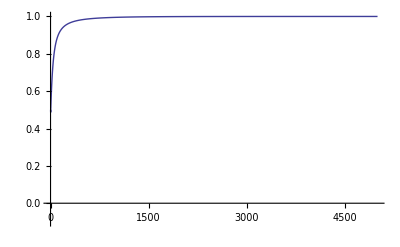

```mathematica
ListLinePlot[out[[3]]+out[[4]],PlotRange->{{0,5000},{-0.1,1.0}}]
```

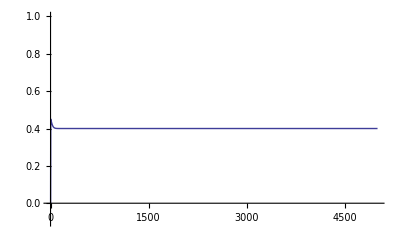

```mathematica
ListLinePlot[out[[10;;11]],PlotRange->{{0,5000},{-0.1,1}}]
```

OK works.